# Skeleton Analysis of Melt Network

## Functions

```mathematica
Clear["Global`*"];
```

getRange[list] returns the range(min and max value) of elements in the list:

```mathematica
getRange:=Function[list,
	min = Min[list];
	max = Max[list];
	{min, max}]
```

move[from, to] add an offset to list from based on the distance between center of range2 and range1:

```mathematica
move:=Function[{from,to},
	range1 = getRange[from];
	range2 = getRange[to];
	offset = (range2⟦1⟧ + range2⟦2⟧-range1⟦1⟧ - range1⟦2⟧)/2;
	res = from + offset;
	res]
```

coordsAlign[coords1, coords2] add offsets to each dimension of coords1 so that coords1 is aligned with coords2. coords1, coords2: N by 3(x,y,z)

```mathematica
coordsAlign:=Function[{coords1,coords2},
	newX = move[coords1⟦;;,1⟧,coords2⟦;;,1⟧];
	newY = move[coords1⟦;;,2⟧,coords2⟦;;,2⟧];
	newZ = move[coords1⟦;;,3⟧,coords2⟦;;,3⟧];
	newCoords1 = {newX,newY,newZ};
	Transpose[newCoords1]]
```

linesToGraph[lines] construct a graph based on the lines

```mathematica
linesToGraph:=Function[{lines},
	graph=Graph[Table[lines⟦i,1⟧<->lines⟦i,2⟧,{i,1,Dimensions[lines]⟦1⟧}]]
]
```

getJunctions[graph] collect all junction nodes(degree >= 3) and their degree from a graph

```mathematica
getJunctions:=Function[{graph},
	ans={};
	For[i=1,i≤VertexCount[graph],i++,
	If[Length[AdjacencyList[graph,i]]>2,AppendTo[ans,{i,Length[AdjacencyList[graph,i]]}]]];
	ans
]
```

mergeScore[ball1, ball2] computes the score which tell whether the two balls should be merged
	ball1: {{x1,y1,z1},r1} 
	ball2: {{x2,y2,z2},r2}

```mathematica
mergeScore := Function[{ball1, ball2},
	r1 = Max[ball1⟦2⟧,ball2⟦2⟧];
	r2 = Min[ball1⟦2⟧,ball2⟦2⟧];
	d = EuclideanDistance[ball1⟦1⟧, ball2⟦1⟧];
	score = (r1 + r2 - d)/(2*r2);
	score
]
```

```mathematica
isDeletableNode:=Function[{numOfAdjacency,degree},
	If[numOfAdjacency == 2 && degree == 2, True, False]
]
```

```mathematica
deletableQ:=Function[{adjacency,degree},
	deleteableList = MapThread[isDeletableNode,{adjacency,degree}]
]
```

```mathematica
deleteNode := Function[{graph, v},
	resGraph = graph;
	neighbors = AdjacencyList[resGraph,v];
	(*If[Length[neighbors] ≠ 2, Return[resGraph]];*)
	
	v1 = neighbors⟦1⟧;
	v2 = neighbors⟦2⟧;
	resGraph = VertexDelete[graph, v];
	resGraph = EdgeAdd[resGraph,v1<->v2];
	resGraph
]
```

```mathematica
(*simplifyGraph := Function[{skelGraph},
	x = skelGraph;
	
	nodesDeg2 = Pick[VertexList[x], deletableQ[VertexDegree[x],Table[Length[AdjacencyList[x]⟦i⟧],{i,Length[AdjacencyList[x]]}]], True];
	While[Length[nodesDeg2] > 0,
		x = deleteNode[x, nodesDeg2⟦1⟧];
		
		nodesDeg2 = Pick[VertexList[x], deletableQ[VertexDegree[x],Table[Length[AdjacencyList[x]⟦i⟧],{i,Length[AdjacencyList[x]]}]], True];
	];
	x
]*)
```

```mathematica
simplifyGraph := Function[{skelGraph},
	x = skelGraph;
	
	nodesDeg2 = Pick[VertexList[x], VertexDegree[x], 2];
	
	While[Length[nodesDeg2] > 0,
		x = deleteNode[x, nodesDeg2⟦1⟧];
		(*degree不变，检查/更新adjacency是不是2 *)
		nodesDeg2 = Pick[VertexList[x], deletableQ[VertexDegree[x],Table[Length[AdjacencyList[x]⟦i⟧],{i,Length[AdjacencyList[x]]}]], True];
	];
	x
]
```

## Function Test

test getRange[list], move[from, to]

```mathematica
list1 = {1,2.5,3.7,4}; list2 = {5,6,7,8};
list1 = move[list1,list2]
```

{5,6.5,7.7,8}

test coordsAlign[coords1, coords2]

```mathematica
coords1={{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}};
coords2={{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}};
coords3=coordsAlign[coords1,coords2]

a = Graphics3D[{
	Red,Point[coords1],
	Green,Point[coords2],
	Red,Opacity[0.3],Ball[coords3,0.1]
}];
Show[a]
```

{{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}}

-Graphics3D-

test linesToGraph[lines] and getJunctions[graph]

```mathematica
(*testLines = {{1,2},{2,3},{1,4},{4,3},{1,3},{3,1}};*)
testLines = {{1,2},{1,2}};
g = linesToGraph[testLines];
GraphPlot3D[g]
VertexDegree[g,1]
EdgeList[g]
(*FindPath[g,2,3, Infinity, All]
s = EdgeContract[g,1<->3];
GraphPlot3D[s]*)
```

-Graphics3D-

2

{1<->2,1<->2}

test deleteNode[graph, v], isDeletableNode, deletableQ

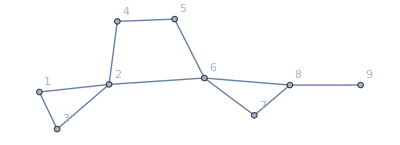

{1,2,3,4,5,6,7,8,9}

{2,4,2,2,2,4,2,3,1}

{2,4,2,2,2,4,2,3,1}

{1,3,4,5,7}

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6,2<->6,8<->9}, VertexLabels -> "Name"]

VertexList[g]
VertexDegree[g]
Table[Length[AdjacencyList[g]⟦i⟧],{i,Length[AdjacencyList[g]]}]

Pick[VertexList[g], VertexDegree[g], 2]
```

test mergeScore

```mathematica
ball1 = {{1,2,3},2};
ball2 = {{4,5,6},6};
mergeScore[ball1, ball2]
```

test isDeletableNode

```mathematica
isDeletableNode[1,2] || False
VertexList[g]
VertexDegree[g]
Table[Length[AdjacencyList[g]⟦i⟧],{i,Length[AdjacencyList[g]]}]
deletableQ[VertexDegree[g],Table[Length[AdjacencyList[g]⟦i⟧],{i,Length[AdjacencyList[g]]}]]
```

False

{1,2,3,4,5,6,7,8}

{2,4,2,2,2,4,2,2}

{2,4,2,2,2,4,2,2}

{True,False,True,True,True,False,True,True}

## Code

### Set working directory

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

### Import data from files

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"];
```

```mathematica
maRawData = Import["data\\scoba12_small.ply","Table"];
maTable = maRawData⟦15;;,;;⟧;

maPoints = maTable⟦;;86117,;;⟧;
maPolygons = maTable⟦363203;;,10;;12⟧ + 1;
```

```mathematica
numOfPoints = 12326;
numOfEdges = 12468;

skelRawData = Import["data\\scoba12_small_skel_0.1.ply","Table"];
skelTable = skelRawData⟦15;;,;;⟧;

skelPoints = skelTable⟦;;numOfPoints,3;;5⟧;
skelLines = skelTable⟦numOfPoints+1;;⟧ + 1;
skelRadius = skelTable⟦;;numOfPoints,2⟧;
```

align coordinates

```mathematica
skelPoints = coordsAlign[skelPoints, maPoints];
```

### Processing data of scoba12 and skeletons

#### Ground Truth

trueJunctions: N by 5 (x, y, z, CN, diameter)

```mathematica
groundTruthTable = groundTruthTable[[1,;;,;;]];
trueJunctions = groundTruthTable[[;;,{4,5,6,10,19}]];
```

#### Median Axes

```mathematica
polygonInCoords = Table[{Blue,Polygon[{maPoints⟦maPolygon⟦1⟧⟧,maPoints⟦maPolygon⟦2⟧⟧,maPoints⟦maPolygon⟦3⟧⟧}]},{maPolygon,maPolygons}];
```

#### Skeleton data

```mathematica
skelGraph = linesToGraph[skelLines];
(*simplifiedGraph = simplifyGraph[skelGraph]*)
junctions = getJunctions[skelGraph];
(*edgeInCoords = Table[{Opacity[1],Red,Thickness[0.004],Line[{skelPoints⟦skelLine⟦1⟧⟧,skelPoints⟦skelLine⟦2⟧⟧}]},{skelLine,skelLines}];*)
junctionBalls = Table[{Ball[skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧]},{i,Dimensions[junctions]⟦1⟧}];
junctionsDataTable = Table[{junctions⟦i,1⟧,junctions⟦i,2⟧,skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧},{i,Dimensions[junctions]⟦1⟧}];
```

$Aborted

## Real-World Data Test & Visualization

validate visualization of median axes

```mathematica
maGraphic = Import["data\\scoba12_small.ply","Graphics3D"];
(*Show[Graphics3D[polygonInCoords],maGraphic]*)
```

validate visualization of skeleton

```mathematica
edgeInCoords = Table[{Opacity[1],Red,Thickness[0.004],Line[{skelPoints⟦skelLine⟦1⟧⟧,skelPoints⟦skelLine⟦2⟧⟧}]},{skelLine,skelLines}];
skelGraphic = Import["data\\scoba12_small_skel_0.1.ply","Graphics3D"];
Show[Graphics3D[edgeInCoords],skelGraphic]
```

-Graphics3D-

show junction balls in median axes

```mathematica
Show[Graphics3D[{edgeInCoords,{Opacity[1],Blue,junctionBalls}}], maGraphic]
Show[Graphics3D[{edgeInCoords,{Opacity[0.5],Blue,junctionBalls}}]]
```

-Graphics3D-

-Graphics3D-

## Issues

### Confusions

#### Missing points and edges in MeshRegion

```mathematica
skelMesh = MeshRegion[skelPoints,Line[skelLines]];
meshPoints = MeshCells[skelMesh,0];
meshLines = MeshCells[skelMesh,1];

Dimensions[skelPoints]
Dimensions[skelLines]

Dimensions[meshPoints]
Dimensions[meshLines]
```

MeshRegion::dgcellr: Degenerate cells including Line[{1767,6061}] have been removed.

{12326,3}

{12468,2}

{11118}

{11260}

### Issues to consider

#### AdjacencyList VS VertexDegree

Basic criteria to merge junction A(x1, y1, r1) and B(x2, y2, r2) as a new junction C(x3, y3, r3):
	1. (x3, y3) = ((x1+x2)/2,(y1+y2)/2) 
	2. r3 = (distance(A, B))/2 + MAX(r1, r2)
	3. new degree = sum of degree (-1 ?)

Center

radius

degree